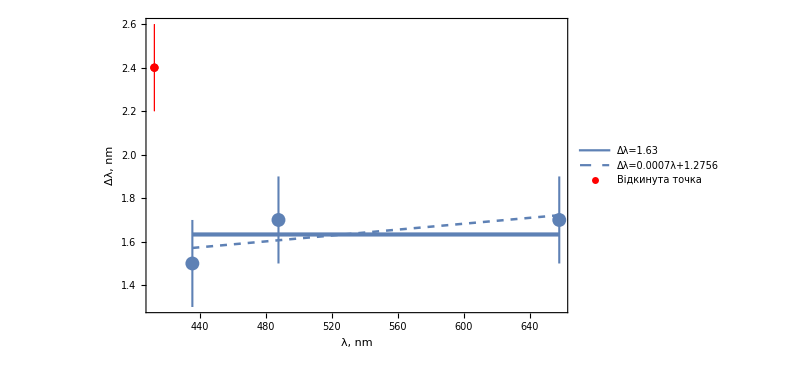

{1.63333,{a→0.,b→1.63333}, | Estimate | Standard Error | t-Statistic | P-Value
a | 0. | 0. | ComplexInfinity | 0.
b | 1.63333 | 0.0942809 | 17.3241 | 0.0367069,{0.,0.0942809}}

{1.2766+0.000676733 x,{a→0.000676733,b→1.2766}, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.000676733 | 0.000726502 | 0.931495 | 0.52257
b | 1.2766 | 0.389128 | 3.28068 | 0.188355,{0.000726502,0.389128}}

```mathematica
SetDirectory[NotebookDirectory[]];
<<data.m;
Needs["ErrorBarPlots`"];
experimental balmer series = {412.6,435.6,487.8,658};
theoretical balmer series = {410.2,434.1,486.1,656.3};
difference list = {experimental balmer series,-(theoretical balmer series - experimental balmer series)}ᵀ;
data = {{435.6,1.5},{487.8,1.6999999999999886},{658,1.7000000000000455}};
data2 = {412.6,2.400000000000034};
errors  = {{.2,.2},{.2,.2},{.2,.2}};
erlist = {data,errors}ᵀ;
plotlist2  ={{{412.6,2.4},ErrorBar[.2,.2]}};
plotlist = {#1,ErrorBar[Sequence@@#2]} &@@@  erlist;
weights = 1/(#1^2+#2^2)&@@@ errors;
fitmodel = NonlinearModelFit[data,0*x+b,{a,b},x,
Weights->weights];
failmodel =  NonlinearModelFit[data,a*x+b,{a,b},x,
Weights->weights];

calibimg=Show[

Plot[{fitmodel[x],failmodel[x]} ,{x,Min@data[[All,1]],Max@data[[All,1]]},ImageSize -> 600,FrameTicksStyle-> 13,PlotRange -> All,
PlotLegends->Placed[{"Δλ=1.63","Δλ=0.0007λ+1.2756"},Scaled[{.74,.60}]],
PlotStyle ->{{Thickness-> 0.005,RGBColor[0.368417,0.506779,0.709798]},{Thickness-> 0.003,RGBColor[0.368417,0.506779,0.709798],Dashed}},Frame -> {True,True,True,True},AxesOrigin-> {400,1.3},FrameLabel->{Style["λ, nm",FontFamily->"Tahoma",FontSize->14,Black],Style["Δλ, nm",FontFamily->"Tahoma",FontSize->14,Black]}],


ErrorListPlot[plotlist, PlotStyle->{AbsolutePointSize[10],AbsoluteThickness[1.5]}, PlotRange -> All],

ErrorListPlot[plotlist2,PlotStyle->{AbsolutePointSize[6],AbsoluteThickness[.8],Red},
PlotLegends->Placed[{"Відкинута точка"},Scaled[{.75,.7}]]]]


Clear[data,weights,errors,erlist,data2,plotlist,plotlist2,difference list];
fitresults = fitmodel[{"BestFit","BestFitParameters","ParameterTable","ParameterErrors"}]
failmodel[{"BestFit","BestFitParameters","ParameterTable","ParameterErrors"}]
```

```mathematica
Export["img\\calib.pdf",calibimg];
```

{1.2766+0.000676733 x,{a→0.000676733,b→1.2766}, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.000676733 | 0.000726502 | 0.931495 | 0.52257
b | 1.2766 | 0.389128 | 3.28068 | 0.188355,{0.000726502,0.389128}}